```mathematica
(*学習率0.3,隠れ層のunit層1,調整回数40000*)
fsigmoid[x_]:=1/(Exp[-x]+1);(*シグモイド関数*)
fout[mW_List,vx_List]:=Module[{vu,vy},
vu=mW.vx;(*リンクの重みmWと前層の出力の行列積で各unitに入る活性ベクトルを計算*)
vy=Map[fsigmoid,vu];(*vuの各成分をsigmoid関数に入れて出力計算*)
Return[vy];
];
```

```mathematica
fforwardBias[vx_]:=Module[{},
gvxa1=Append[vx,1];
gvy1=fout[gW1,gvxa1];
gvy1a1=Append[gvy1,1];
gvy2=gW2.gvy1a1;(*回帰のため変更*)
Return[gvy2];
];
```

```mathematica
fbackwardBias[vx_List,vy1_List,vy2_List,vt_List,eta_]:=Module[{vs,vs2,vs1,mp2,mp1},
vs2=vy2-vt;(*回帰のため変更*)
vs1=(vs2.gW2)*gvy1a1*(1-gvy1a1);
vs1d1=Drop[vs1,-1];
gW2=gW2-eta*Outer[Times,vs2,gvy1a1];
gW1=gW1-eta*Outer[Times,vs1d1,gvxa1];
];
```

```mathematica
flearnrepeatBias[eta_,kurikaesiSuu_]:=Module[
{ii,k,vx,vy,vs2,vs1,vt,errtbl},(*作業用変数のリスト*)
errtbl=Table[{},{k,1,Length[gKyousiList]}];(*正答ごとの誤差を入れるリストを用意*)
For[ii=1,ii≤kurikaesiSuu,ii++,(*調整を繰り返す．学習の主要部分*)
k=RandomInteger[{1,Length[gKyousiList]}];(*入力ー正答ペアの番号kをランダムに取る*)
vx=gInpList[[k]];vt=gKyousiList[[k]];(*k番目の入力と教師信号を取り出す．*)
vy=fforwardBias[vx];(*biasのため変更*)

errtbl[[k]]=Append[errtbl[[k]],sqrt[(vy-vt).(vy-vt)]];(*出力と正答間の誤差を入れる*)
fbackwardBias[vx,gvy1,vy,vt,eta];(*biasのため変更*)
];(*以上をkurikaesiSuuだけ繰り返す*)

gerrtbl=errtbl;(*誤差のリストをグローバル変数gerrtblに残しておく*)
vylist=Table[fforwardBias[vx],{vx,gInpList}];(*学習後の重みで計算*)
Return[vylist];(*その結果を返り値とする*)
];
```

```mathematica
data=(*入力のxと出力のyからなる教師信号*)
{{0.0,0.349486},{0.111111,0.830839},
{0.222222,1.007332},{0.333333,0.971507},
{0.444444,0.133066},{0.555556,0.166823},
{0.666667,-0.848307},{0.777778,-0.445686},
{0.888889,-0.563567},{1.000000,0.261502}
};
```

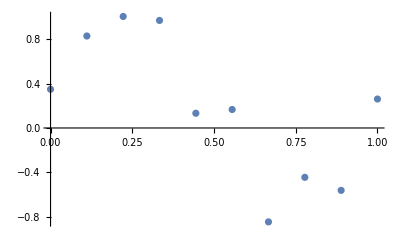

```mathematica
dataplot=ListPlot[data]
```

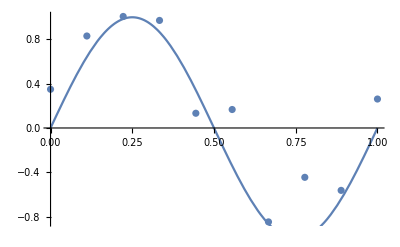

```mathematica
(*sinと比較．noiseの分だけずれている*)
sinplot=Plot[Sin[2*Pi*x],{x,0,1}];Show[dataplot,sinplot]
```

```mathematica
gInpList=Table[{data[[i,1]]},{i,1,Length[data]}]
(*各入力点．括弧で囲んでそれぞれリスト(要素数1)とする*)
```

{{0.},{0.111111},{0.222222},{0.333333},{0.444444},{0.555556},{0.666667},{0.777778},{0.888889},{1.}}

```mathematica
gKyousiList=Table[{data[[i,2]]},{i,1,Length[data]}](*上記入力点に対する教師信号．やはりそれぞれリスト(要素数1)にする*)
```

{{0.349486},{0.830839},{1.00733},{0.971507},{0.133066},{0.166823},{-0.848307},{-0.445686},{-0.563567},{0.261502}}

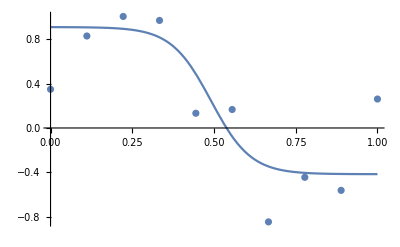

```mathematica
gn0=1;gn1=1;gn2=1;
SeedRandom[1234];
gW1=RandomReal[{-0.1,0.1},{gn1,gn0+1}];
gW2=RandomReal[{-0.1,0.1},{gn2,gn1+1}];
geta=0.3;gkaisuu=40000;(*教師信号が多いので繰り返しもたくさんいる*)
flearnrepeatBias[geta,gkaisuu];
kekkaplot=Plot[fforwardBias[{x}][[1]],{x,0,1},PlotRange->All];(*学習結果の関数*)
Print@Show[dataplot,kekkaplot];
```

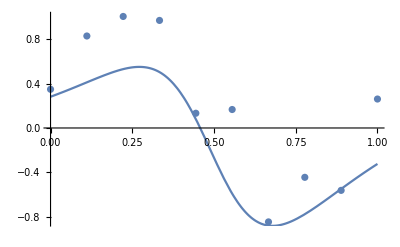

```mathematica
(*中間層unit数2．上のunit数1の場合のものを一通りコピペし，gn1の値だけを変えた*)
gn0=1;gn1=2;gn2=1;
SeedRandom[1234];
gW1=RandomReal[{-0.1,0.1},{gn1,gn0+1}];
gW2=RandomReal[{-0.1,0.1},{gn2,gn1+1}];
geta=0.3;gkaisuu=40000;(*教師信号が多いので繰り返しもたくさんいる*)
flearnrepeatBias[geta,gkaisuu];
kekkaplot=Plot[fforwardBias[{x}][[1]],{x,0,1},PlotRange->All];(*学習結果の関数*)
Print@Show[dataplot,kekkaplot];
```

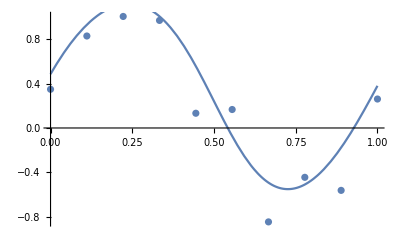

```mathematica
(*中間層unit数3．上のunit数1の場合のものを一通りコピペし，gn1の値だけを変えた*)
gn0=1;gn1=3;gn2=1;
SeedRandom[1234];
gW1=RandomReal[{-0.1,0.1},{gn1,gn0+1}];
gW2=RandomReal[{-0.1,0.1},{gn2,gn1+1}];
geta=0.3;gkaisuu=40000;(*教師信号が多いので繰り返しもたくさんいる*)
flearnrepeatBias[geta,gkaisuu];
kekkaplot=Plot[fforwardBias[{x}][[1]],{x,0,1},PlotRange->All];(*学習結果の関数*)
Print@Show[dataplot,kekkaplot];
```

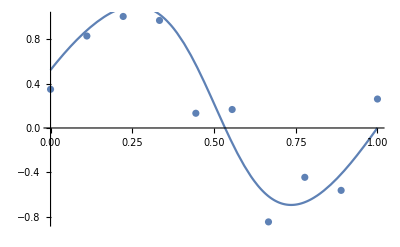

```mathematica
(*中間層unit数10．上のunit数1の場合のものを一通りコピペし，gn1の値だけを変えた*)
gn0=1;gn1=10;gn2=1;
SeedRandom[1234];
gW1=RandomReal[{-0.1,0.1},{gn1,gn0+1}];
gW2=RandomReal[{-0.1,0.1},{gn2,gn1+1}];
geta=0.3;gkaisuu=40000;(*教師信号が多いので繰り返しもたくさんいる*)
flearnrepeatBias[geta,gkaisuu];
kekkaplot=Plot[fforwardBias[{x}][[1]],{x,0,1},PlotRange->All];(*学習結果の関数*)
Print@Show[dataplot,kekkaplot];
```

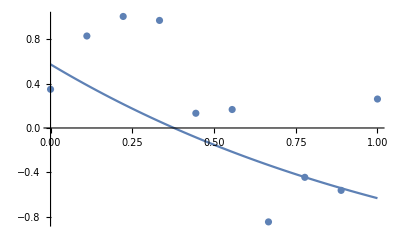

```mathematica
(*中間層unit数50．上のunit数1の場合のものを一通りコピペし，gn1の値だけを変えた*)
gn0=1;gn1=50;gn2=1;
SeedRandom[1234];
gW1=RandomReal[{-0.1,0.1},{gn1,gn0+1}];
gW2=RandomReal[{-0.1,0.1},{gn2,gn1+1}];
geta=0.3;gkaisuu=40000;(*教師信号が多いので繰り返しもたくさんいる*)
flearnrepeatBias[geta,gkaisuu];
kekkaplot=Plot[fforwardBias[{x}][[1]],{x,0,1},PlotRange->All];(*学習結果の関数*)
Print@Show[dataplot,kekkaplot];
```

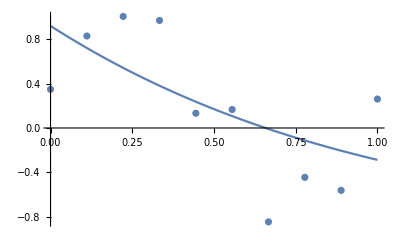

```mathematica
(*中間層unit数25．上のunit数1の場合のものを一通りコピペし，gn1の値だけを変えた*)
gn0=1;gn1=25;gn2=1;
SeedRandom[1234];
gW1=RandomReal[{-0.1,0.1},{gn1,gn0+1}];
gW2=RandomReal[{-0.1,0.1},{gn2,gn1+1}];
geta=0.3;gkaisuu=40000;(*教師信号が多いので繰り返しもたくさんいる*)
flearnrepeatBias[geta,gkaisuu];
kekkaplot=Plot[fforwardBias[{x}][[1]],{x,0,1},PlotRange->All];(*学習結果の関数*)
Print@Show[dataplot,kekkaplot];
```

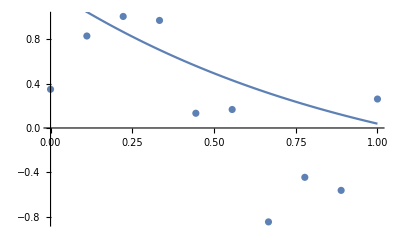

```mathematica
(*中間層unit数18．上のunit数1の場合のものを一通りコピペし，gn1の値だけを変えた*)
gn0=1;gn1=18;gn2=1;
SeedRandom[1234];
gW1=RandomReal[{-0.1,0.1},{gn1,gn0+1}];
gW2=RandomReal[{-0.1,0.1},{gn2,gn1+1}];
geta=0.3;gkaisuu=40000;(*教師信号が多いので繰り返しもたくさんいる*)
flearnrepeatBias[geta,gkaisuu];
kekkaplot=Plot[fforwardBias[{x}][[1]],{x,0,1},PlotRange->All];(*学習結果の関数*)
Print@Show[dataplot,kekkaplot];
```